# info-graphics

P. Huft

```mathematica
imagedir=FileNameJoin[{NotebookDirectory[],"images\\"}];
SetDirectory[imagedir];
```

```mathematica
xnum=ynum=10;
```

```mathematica
num = √(xnum ynum); 
atom[i_,excited_]:=If[excited,Graphics[{Orange,Disk[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}],Graphics[{Blue,Circle[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}]];
r[i_,j_] :=Graphics[{Red,Line[{a{Mod[i-1,num], Floor[(i-1)/num]},a{Mod[j-1,num],Floor[(j-1)/num]}}]}];
gridpts = Table[atom[i,False],{i,Range[num^2]}];
```

Range::range: Range specification in Range[xnum ynum] does not have appropriate bounds.

Table::iterb: Iterator {i,Range[xnum ynum]} does not have appropriate bounds.

```mathematica
atomGraphic = Join[Table[Graphics3D[{Orange,Sphere[{i,j,0},0.1]}],{i,1,xnum},{j,1,ynum}],Table[Graphics3D[{Red,Arrow[{{i,j,-0.5},{i,j,0.5}}]}],{i,1,xnum},{j,1,ynum}]];
```

```mathematica
graphic =Show[atomGraphic,Boxed-> False]
```

-Graphics3D-

```mathematica
depth=5;
atomGraphic = Table[Graphics3D[{Orange,Sphere[{i,j,k},0.1]}],{i,1,xnum},{j,1,ynum},{k,1,depth}];
```

```mathematica
graphic=Show[atomGraphic,Boxed->False]
```

-Graphics3D-

```mathematica
Export[ToString[StringForm["graphic_3D_atom_dipoles_``x``x``.png",xnum,ynum,depth]],graphic,ImageResolution-> 300]
```

graphic_3D_atom_dipoles_10x10x5.png

```mathematica
reds = Table[Hue[1,1.0/(1+(0.5i)^2)],{i,{-2,-1,0,1,2}}]
```

{Hue[1, 0.5],Hue[1, 0.8],Hue[1, 1.],Hue[1, 0.8],Hue[1, 0.5]}

```mathematica
plts={};(*Table[Plot[{2 √(1+z^2)-10i,-2 √(1+z^2)-10i},{z,-5,5},PlotStyle->Hue[1,1./(1+(0.5i)^2)],Filling->{1-> {2}},Axes->False,PlotRange->{-50,50},ImageSize->Large],{i,{-2,-1,0,1,2}}];*)
AppendTo[plts,Plot[Evaluate[{If[z>0,0.8*2 √(1+z^2)-10i],If[z>0,-0.8*2 √(1+z^2)-10i]}/.i-> 1],{z,-5,5},PlotStyle->Hue[0.54,1],Filling->{1-> {2}},FillingStyle-> Opacity[0.9],Axes->False,ImageSize->Large]];
AppendTo[plts,Plot[Evaluate[{If[z<=0,0.8*2 √(1+z^2)-10i],If[z<=0,-0.8*2 √(1+z^2)-10i]}/.i-> 1],{z,-5,5},PlotStyle->Hue[1,0.8],Filling->{1-> {2}},FillingStyle-> Opacity[0.9],Axes->False,ImageSize->Large]];
```

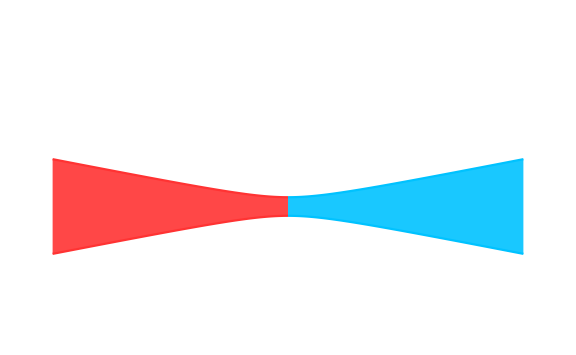

```mathematica
plt =Show[plts,ImageSize-> Large,PlotRange->{{-5,5},{-30,20}},Axes->False]
```

```mathematica
plts={};
AppendTo[plts,Plot[Evaluate[{If[z>0,0.8*2 √(1+z^2)-10i],If[z>0,-0.8*2 √(1+z^2)-10i]}/.i-> 1],{z,-5,5},PlotStyle->Hue[0.54,1],Filling->{1-> {2}},FillingStyle-> Opacity[0.9],Axes->False,ImageSize->Large]];
AppendTo[plts,Plot[Evaluate[{If[z<=0,0.8*2 √(1+z^2)-10i],If[z<=0,-0.8*2 √(1+z^2)-10i]}/.i-> 1],{z,-5,5},PlotStyle->Hue[1,0.8],Filling->{1-> {2}},FillingStyle-> Opacity[0.9],Axes->False,ImageSize->Large]];
```

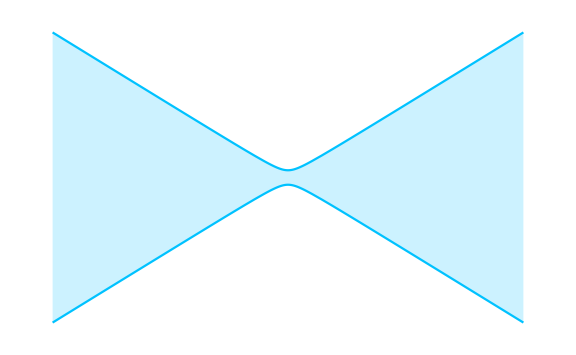

```mathematica
plt=Plot[{2 √(1+z^2)-10,-2 √(1+z^2)-10},{z,-20,20},PlotStyle->Hue[0.54,1],Filling->{1-> {2}},Axes->False,ImageSize->Large]
```

```mathematica
(*(*Export["blue_beam_expanding.png",plt,ImageResolution-> 600,Background-> None]*)*)
```

blue_beam_expanding.png

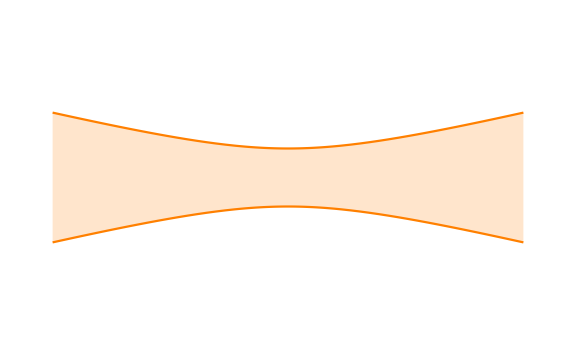

```mathematica
color=ColorData["DarkRainbow"][[-1]][0.9];
color=Orange;
plt=Plot[{2 √(1+z^2),-2 √(1+z^2)},{z,-2,2},PlotStyle->color,Filling->{1-> {2}},Axes->False,ImageSize->Large,PlotRange->{-10,10}]
```

0.45

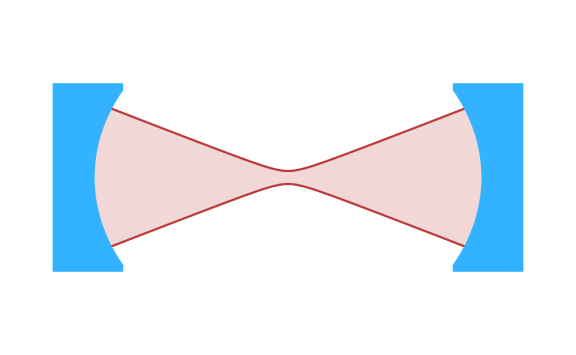

```mathematica
rcav = 11.5;
α=0.45
beam=Plot[{α √(1+z^2),-α √(1+z^2)},{z,-rcav,rcav},PlotStyle->ColorData["DarkRainbow"][[-1]][0.9],Filling->{1-> {2}},Axes->True,ImageSize->Large];
(*cav=Graphics[{Blue,BoundaryDiscretizeRegion[RegionDifference[Rectangle[{-15,-9},{-8,9}],Disk[{0,
0},rcav,{Pi/2,3Pi/2}]],MaxCellMeasure->.1]}];*)
(*cav=Graphics[{Blue,BoundaryDiscretizeRegion[RegionDifference[Rectangle[{-16,-9},{-8,9}],Disk[{0,
0},rcav,{Pi/2,3Pi/2}]],MaxCellMeasure->.1]}];*)
color = RGBColor[51/255,179/255,1];
r=6.5;
xmax=14;xmin=9.8;
cav=Graphics[{color,BoundaryDiscretizeRegion[RegionDifference[Rectangle[{-xmax,-r},{-xmin,r}],Disk[{0,
0},rcav,{Pi/2,3Pi/2}]],MaxCellMeasure->.1],color,BoundaryDiscretizeRegion[RegionDifference[Rectangle[{xmin,-r},{xmax,r}],Disk[{0,
0},rcav,{-Pi/2,Pi/2}]],MaxCellMeasure->.1]}];
plt=Show[beam,cav,PlotRange->{-10,10},Axes->False]
```

```mathematica
Export["cavity_with_mode.svg",plt,Background-> None]
```

cavity_with_mode.svg

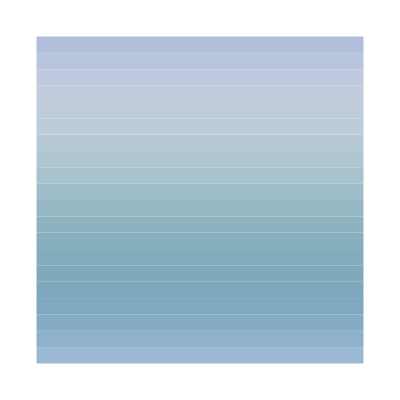

```mathematica
Graphics[{Blue,ChartElementData["GradientRectangle","ColorScheme"->"Aquamarine","GradientOrigin"->Top][{{0,1},{0,1}}]}]
```

```mathematica
ColorData
```

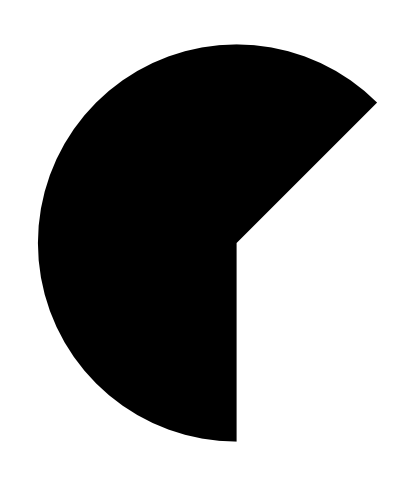

```mathematica
Graphics[{Disk[{0,
0},10,{Pi/4,3Pi/2}]}]
```

```mathematica
ChartElementData["GradientRectangle","GradientOrigin"->Top][{{0,1},{0,1}}]
```

{{EdgeForm[],GraphicsComplex[{{0.,0.},{0.,0.0909091},{0.,0.181818},{0.,0.272727},{0.,0.363636},{0.,0.454545},{0.,0.545455},{0.,0.636364},{0.,0.727273},{0.,0.818182},{0.,0.909091},{0.,1.},{1.,0.},{1.,0.0909091},{1.,0.181818},{1.,0.272727},{1.,0.363636},{1.,0.454545},{1.,0.545455},{1.,0.636364},{1.,0.727273},{1.,0.818182},{1.,0.909091},{1.,1.}},Polygon[…],VertexColors→{{0.645624,0.660807,0.778286},{0.737204,0.759043,0.907105},{0.698177,0.714595,0.841627},{0.762341,0.748974,0.784665},{0.77615,0.762081,0.645243},{0.861627,0.773511,0.417147},{0.918547,0.79826,0.409216},{0.899919,0.722681,0.302067},{0.885293,0.656449,0.289156},{0.869709,0.582691,0.275181},{0.853407,0.503288,0.26041},{0.674205,0.423758,0.242374},{0.645624,0.660807,0.778286},{0.737204,0.759043,0.907105},{0.698177,0.714595,0.841627},{0.762341,0.748974,0.784665},{0.77615,0.762081,0.645243},{0.861627,0.773511,0.417147},{0.918547,0.79826,0.409216},{0.899919,0.722681,0.302067},{0.885293,0.656449,0.289156},{0.869709,0.582691,0.275181},{0.853407,0.503288,0.26041},{0.674205,0.423758,0.242374}}]},{FaceForm[],Rectangle[{0,0},{1,1}]}}

```mathematica
a=1;b=5;
Graphics[{Rectangle[{5,5}],Blue,Rectangle[{-5,-5}],Green,BoundaryDiscretizeRegion[RegionDifference[ChartElementData["GradientRectangle","GradientOrigin"->Top][{{0,1},{0,1}}],Disk[{-10,
0},{3,20},{Pi/2,3Pi/2}]],MaxCellMeasure->.1]}]
```

RegionDifference::reg: {{EdgeForm[],GraphicsComplex[{{0.,0.},{0.,0.0909091},{0.,0.181818},{0.,0.272727},{0.,0.363636},{0.,0.454545},{0.,0.545455},{0.,0.636364},{0.,0.727273},{0.,0.818182},«14»},«7»[«1»],VertexColors→{{0.645624,0.660807,0.778286},{0.737204,0.759043,0.907105},{0.698177,0.714595,0.841627},{0.762341,0.748974,0.784665},{0.77615,0.762081,0.645243},{«1»},«1»,{0.899919,0.722681,0.302067},{0.885293,0.656449,0.289156},{0.869709,0.582691,0.275181},«14»}]},«1»} is not a correctly specified region.

BoundaryDiscretizeRegion::regp: A correctly specified region expected at position 1 of BoundaryDiscretizeRegion[RegionDifference[{{EdgeForm[],GraphicsComplex[{{0.,0.},{0.,0.0909091},{0.,0.181818},{0.,0.272727},{0.,0.363636},{0.,0.454545},{0.,0.545455},{0.,0.636364},{0.,0.727273},{0.,0.818182},«14»},Polygon[{{«4»},{«4»},{«4»},{«4»},{«4»},{«4»},{«4»},{«4»},{«4»},{«4»},«1»}],VertexColors→{{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},«14»}]},{FaceForm[],Rectangle[{0,0},{1,1}]}},Disk[{-10,0},{3,20},{π/2,(3 π)/2}]],MaxCellMeasure→0.1].

-Graphics-

```mathematica
cav
```

BooleanRegion[#1&&!#2&,{Rectangle[{-18,-26},{-10,26}],Disk[{-10,0},{3,20},{π/2,(3 π)/2}]}]

```mathematica
Export["deepred_beam_expanding.svg",plt,Background-> None]
```

deepred_beam_expanding.svg

```mathematica
Export["FORT_sites.png",plt,ImageResolution-> 600]
```

FORT_sites.png

```mathematica
ColorData["DarkRainbow"][[-1]][0.9]
```

RGBColor[0.72987, 0.239399, 0.230961]

```mathematica
Hue[0.54,0.8]
```

Hue[0.54, 0.8]

```mathematica
Hue[1,0.8]
```

Hue[1, 0.8]

```mathematica
1.7*^9/10
```

1.7×10^8

```mathematica
{{-2,1},{-1,1},{-1,0.3},{1,0.3},{1,1},{1,2}}
```

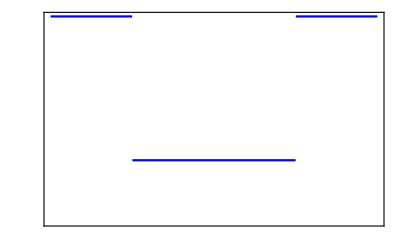

```mathematica
plt=Plot[Piecewise[{{1,x<-1},{0.3,-1<=x≤1},{1,x>1}}],{x,-2,2},Frame->{True,True,False,False},Axes-> False,PlotRange->{0,1},FrameTicks->None,PlotStyle->Blue]
```

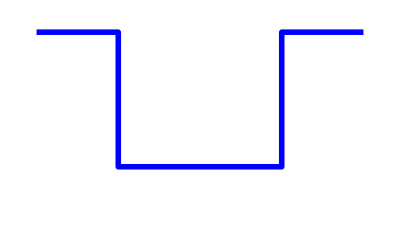

```mathematica
plt=ListPlot[{{-2,1},{-1,1},{-1,0.3},{1,0.3},{1,1},{1,1},{2,1}},Frame->{False,False,False,False},Axes-> False,PlotRange->{0,1.05},FrameTicks->None,PlotStyle->Directive[Blue,AbsoluteThickness[4]],Joined->True]
```

```mathematica
Export["sq_pulse_thick4.png",plt,ImageResolution-> 300,Background-> None]
```

sq_pulse_thick4.png

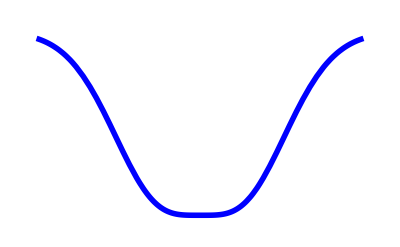

```mathematica
plt=Plot[(1-Exp[-x^2])^2,{x,-2,2},Frame->{False,False,False,False},Axes-> False,PlotRange->{-0.05,1.05},FrameTicks->None,PlotStyle->Directive[Blue,AbsoluteThickness[4]]]
```

```mathematica
Export["minus_gaussian_thick4.svg",plt,ImageResolution-> 300,Background-> None]
```

minus_gaussian_thick4.svg

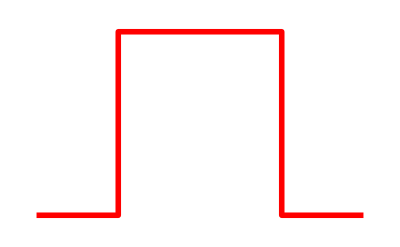

```mathematica
plt=ListPlot[{{-2,0},{-1,0},{-1,1},{1,1},{1,0},{2,0}},Frame->{False,False,False,False},Axes-> False,PlotRange->{-0.05,1.05},FrameTicks->None,PlotStyle->Directive[Red,AbsoluteThickness[4]],Joined->True]
```

```mathematica
Export["sq_pulse_positive_thick4.png",plt,ImageResolution-> 300,Background-> None]
```

sq_pulse_positive_thick4.png

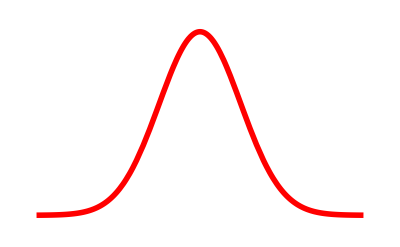

```mathematica
plt=Plot[Exp[-2 x^2],{x,-2,2},Frame->{False,False,False,False},Axes-> False,PlotRange->{-0.05,1.05},FrameTicks->None,PlotStyle->Directive[Red,AbsoluteThickness[4]]]
```

```mathematica
Export["gaussian_thick4.svg",plt,ImageResolution-> 300,Background->None]
```

gaussian_thick4.svg

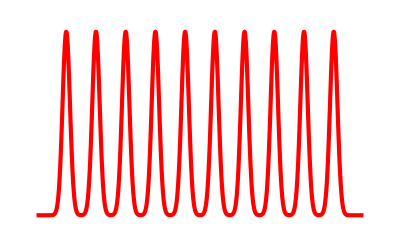

```mathematica
plt=Plot[Sum[Exp[-2(x-4 (j-1))^2],{j,Range[10]}],{x,-4,2*20},Frame->{False,False,False,False},Axes-> False,PlotRange->{-0.05,1.05},FrameTicks->None,PlotStyle->Directive[Red,AbsoluteThickness[3]]]
```

```mathematica
Export["gaussian_array10_thick3.png",plt,ImageResolution-> 300]
```

gaussian_array10_thick3.png

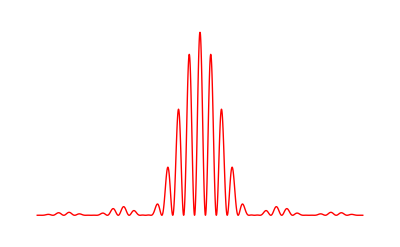

```mathematica
λ=1*^-6;L=0.5;d=0.5*^-3;a=1*^-4;
plt=Plot[(Cos[(π d)/λ x/L] Sin[(π a)/λ x/L]/((π a)/λ x/L))^2,{x,-30*(λ L)/(2d),30*(λ L)/(2d)},Frame->{False,False,False,False},Axes-> False,PlotRange->{-0.05,1.05},FrameTicks->None,PlotStyle->Directive[Red,AbsoluteThickness[1]]]
```

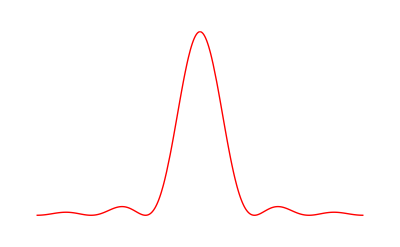

```mathematica
plt=Plot[(Sin[(π a)/λ x/L]/((π a)/λ x/L))^2,{x,-30*(λ L)/(2d),30*(λ L)/(2d)},Frame->{False,False,False,False},Axes-> False,PlotRange->{-0.05,1.05},FrameTicks->None,PlotStyle->Directive[Red,AbsoluteThickness[1]]]
```

General::munfl: Exp[-799.928] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1151.91] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1567.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

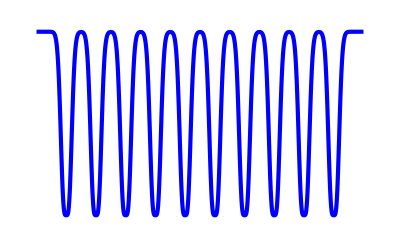

```mathematica
plt=Plot[(1-Sum[Exp[-(x-4 (j-1))^2/0.5],{j,Range[10]}])^2,{x,-4,2*20},Frame->{False,False,False,False},Axes-> False,PlotRange->{-0.05,1.05},FrameTicks->None,PlotStyle->Directive[Blue,AbsoluteThickness[3]]]
```

```mathematica
Export["minus_gaussian_array10_thick3.svg",plt,ImageResolution-> 300,Background-> None]
```

minus_gaussian_array10_thick3.svg

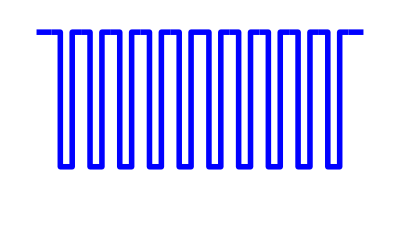

```mathematica
plt=Show[ListPlot[Table[{{-2+i,1},{-0.8+i,1},{-0.8+i,0.3},{0.8+i,0.3},{0.8+i,1},{2+i,1}},{i,4*Range[10]}],Frame->{False,False,False,False},Axes-> False,PlotRange->{0,1.05},FrameTicks->None,PlotStyle->Directive[Blue,AbsoluteThickness[4]],Joined->True],ListPlot[{{0,1},{2,1}},PlotStyle->Directive[Blue,AbsoluteThickness[4]],Joined->True],ListPlot[{{42,1},{44,1}},PlotStyle->Directive[Blue,AbsoluteThickness[4]],Joined->True],PlotRange-> {{0,44},{0,1.05}}]
```

```mathematica
Export["minus_tophat_array10.png",plt,ImageResolution-> 300,Background-> None]
```

minus_tophat_array10.png

```mathematica
xnum=ynum=10;
gridcircs = Join[Table[Graphics[{White,Disk[{i,j},0.25]}],{i,1,xnum},{j,1,ynum}]];
plt=Show[gridcircs]
```

-Graphics-

```mathematica
Manipulate[RGBColor[r,g,b],{r,0,1},{g,0,1},{b,0,1}]
```

```mathematica
Export["grid_array10x10_white.png",plt,ImageResolution-> 300,Background-> None]
```

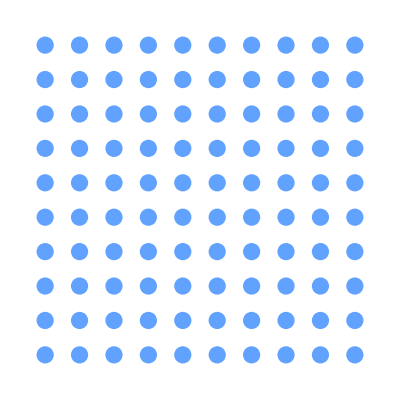

```mathematica
xnum=ynum=10;
gridcircs = Join[Table[Graphics[{RGBColor[0.38,0.634,1],Disk[{i,j},0.25]}],{i,1,xnum},{j,1,ynum}]];
plt=Show[gridcircs]
```

```mathematica
Export["grid_array10x10_mediumblue.png",plt,ImageResolution-> 300,Background-> None]
```

grid_array10x10_mediumblue.png

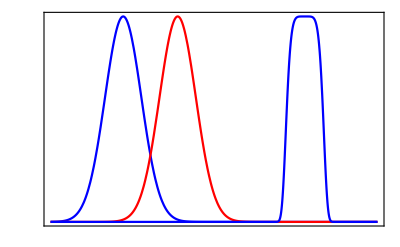

```mathematica
plt=Plot[{Exp[-2 x^2],Exp[-2(x-1.5)^2],Exp[-40(x-5)^6]},{x,-2,7},Frame->{True,True,False,False},Axes-> False,PlotRange->{0,1},FrameTicks->None,PlotStyle->{Blue,Red}]
```

```mathematica
Export["stirap_excitation_stim_pulses.png",plt,ImageResolution-> 300]
```

stirap_excitation_stim_pulses.png

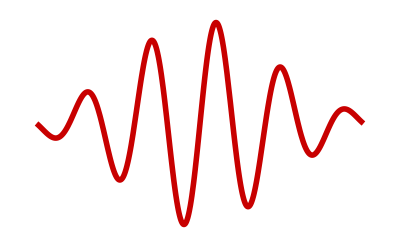

```mathematica
color = RGBColor[200/255,0,0];
(*color = Gray;*)
plt=Plot[Exp[-x^2]Sin[10x],{x,-π/2,π/2},PlotStyle->Directive[color,Thickness-> 0.01],Axes->False,PlotRange->All]
```

```mathematica
Export["photon_packet_decay_red2.svg",plt,Background-> None]
```

photon_packet_decay_red2.svg

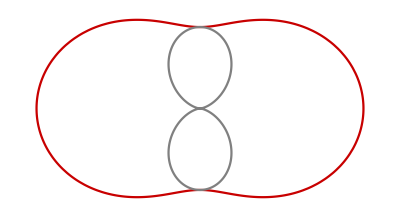

```mathematica
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
pi ={0,-Sin[θ],0};
rh =ⅇ^(ⅈ ϕ)/(√2){0,Cos[θ],ⅈ};
lh =ⅇ^(-ⅈ ϕ)/(√2){0,Cos[θ],-ⅈ};
plt=PolarPlot[{(lh.conj[lh]+rh.conj[rh])3/(8π),pi.conj[pi] 3/(8π)},{θ,0,2π},(*PlotLegends->{"P(σ_+ or σ_-)","P(π)"},*)PlotStyle->{RGBColor[200/255,0,0],Gray},Axes-> False]
```

```mathematica
Export["dipole_emission.svg",plt,Background-> None]
```

dipole_emission.svg

```mathematica
Graphics[]
```

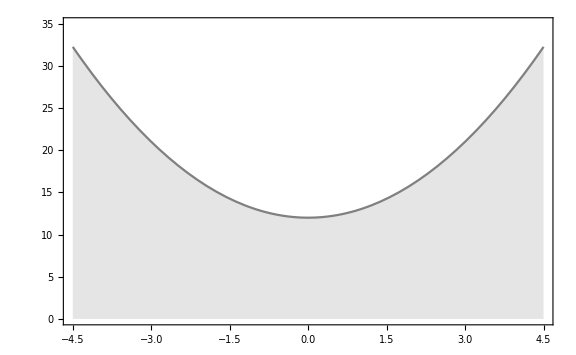

```mathematica
plt=Plot[{z^2+12},{z,-4.5,4.5},PlotStyle->,Filling->Axis,Axes->False,ImageSize->Large,PlotRange->{0,35},Axes->False]
```

```mathematica
xnum=5;
ynum=2;
gridcircs = Join[Table[Graphics[{RadialGradientFilling[{Red,White}],Disk[{i,j},0.25]}],{i,1,xnum},{j,1,ynum}]];
gridcircs1 = Join[Table[Graphics[{RadialGradientFilling[{Green,White}],Disk[{i,j},0.25]}],{i,1,xnum},{j,ynum+1,ynum+1}]];gridcircs2 =Join[Table[Graphics[{RadialGradientFilling[{Red,White}],Disk[{i,j},0.25]}],{i,1,xnum},{j,ynum+2,2*ynum+1}]];
plt=Show[gridcircs1]
```

-Graphics-

```mathematica
Export["atomrow_five_green.svg",plt,Background-> None]
```

atomrow_five_green.svg

```mathematica
xnum=ynum=6;
gridcircs = Join[Table[Graphics[{RadialGradientFilling[{Red,White}],Disk[{i+0.5,j+0.5},0.25]}],{i,1,xnum},{j,1,ynum}]];
gridcircs1 = Join[Table[Graphics[{RadialGradientFilling[{Green,White}],Disk[{i,j},0.25]}],{i,2,xnum},{j,2,ynum}]];
plt=Show[gridcircs,gridcircs1]
```

-Graphics-

```mathematica
Export["atomarray_red_green2.svg",plt,ImageResolution-> 600,Background-> None]
```

atomarray_red_green2.svg

```mathematica
xnum=ynum=6;
gridcircs = Join[Table[Graphics[{RadialGradientFilling[{Red,White}],Disk[{i+0.5,j+0.5},0.25]}],{i,1,xnum},{j,1,ynum}]];
gridcircs1 = Join[Table[Graphics[{RadialGradientFilling[{Green,White}],Disk[{i,j},0.25]}],{i,2,ynum},{j,2,3}]];
oneatom = Graphics[{RadialGradientFilling[{Green,White}],Disk[{4,4},0.25]}];
gridcircs2 = Join[Table[Graphics[{RadialGradientFilling[{Green,White}],Disk[{i,j},0.25]}],{i,2,ynum},{j,5,6}]];
plt=Show[gridcircs,gridcircs1,gridcircs2]
```

-Graphics-

```mathematica
Export["atomarray_red_green4.svg",plt,ImageResolution-> 600,Background-> None]
```

atomarray_red_green4.svg

```mathematica
oneatom
```

```mathematica
xnum=1;
gridcircs = Join[Table[Graphics[{RadialGradientFilling[{Green,White}],Disk[{i+0.5,j+0.5},0.25]}],{i,1,xnum},{j,1,1}]];
plt=Show[gridcircs]
Export["one_atom_green.svg",plt,Background-> None]
```

-Graphics-

one_atom_green.svg

```mathematica
plt=Plot3D[0.6(1-Exp[-(x^2+y^2)])^2+0.4Exp[-2((x-5/√2)^2+(y-5/√2)^2)0.67^2],{x,-2,5.5},{y,-2,5.5},BoxRatios->{1, 1, 1},PlotRange->All,Boxed->False,ColorFunction->GrayLevel,Axes->False,AxesLabel->{"x","y","Intensity"}]
```

-Graphics3D-

```mathematica
Export["bright_dark_trap_plot_contour.svg",plt,Background-> None]
```

bright_dark_trap_plot_contour.svg

```mathematica
2.998*10^8*27*^-9
```

8.0946